```mathematica
tnorm[x_,y_,z_]:=x+y-z
boundary[x_,y_,z_]:=GCD[x,y+z]+GCD[y,z+x]+GCD[z,x+y]
boundaryBeta[x_,y_,z_]:=GCD[y,z+x]
genus[x_,y_,z_]:=(tnorm[x,y,z]+2-boundary[x,y,z])/2
dila[x_,y_,z_]:=Module[{theta},
					theta[t_]=Power[t,x+y-z]-t^x-t^y-Power[t,x-z]-Power[t,y-z]+1;
				Max[Abs[t/.Solve[theta[t]==0,t,Reals]]]]
```

```mathematica
normDilaUnfilled[x_,y_,z_]:=tnorm[x,y,z]*Log[dila[x,y,z]]
```

```mathematica
normDilaFilled[x_,y_,z_]:=(tnorm[x,y,z]-boundary[x,y,z])*Log[dila[x,y,z]]
normDilaFilledBeta[x_,y_,z_]:=(tnorm[x,y,z]-boundaryBeta[x,y,z])*Log[dila[x,y,z]]
```

```mathematica
p1=ParametricPlot3D[{1,t,t},{t,0,1}];
p2=ParametricPlot3D[{1-t,1,1-t},{t,0,1}];
p3=ParametricPlot3D[{0,1-t,-t},{t,0,1}];
p4=ParametricPlot3D[{t,0,-1+t},{t,0,1}];
p5=ParametricPlot3D[{2*t,0,0},{t,0,1},PlotStyle->Red];
p6=ParametricPlot3D[{2*t,2*t,2*t},{t,0,1},PlotStyle->Red];
p7=ParametricPlot3D[{0,2*t,0},{t,0,1},PlotStyle->Red];
p8=ParametricPlot3D[{0,0,-2*t},{t,0,1},PlotStyle->Red];
p9=ParametricPlot3D[{2*t,2*t,-2*t},{t,0,1},PlotStyle->Green];
```

```mathematica
Show[p1,p2,p3,p4,p5,p6,p7,p8,p9,Graphics3D[R],PlotRange->{{-2,2},{-2,2},{-2,2}}]
```

-Graphics3D-

```mathematica
minimal=normDilaUnfilled[1,1,0]
N[minimal,10]
```

2 Log[2+√3]

2.633915794

```mathematica
ContourPlot3D[Exp[x+y+z]-Exp[x]-Exp[y]-Exp[x-z]-Exp[y-z]+1==0,{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
Solve[Exp[x+y+z]-Exp[x]-Exp[y]-Exp[x-z]-Exp[y-z]+1==0,z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→Log[1/2 ⅇ^(-x-y) (-1+ⅇ^x+ⅇ^y-√(-4 ⅇ^(x+y) (-ⅇ^x-ⅇ^y)+(1-ⅇ^x-ⅇ^y)^2))]},{z→Log[1/2 ⅇ^(-x-y) (-1+ⅇ^x+ⅇ^y+√(-4 ⅇ^(x+y) (-ⅇ^x-ⅇ^y)+(1-ⅇ^x-ⅇ^y)^2))]}}

```mathematica
G[x_,y_]:=x+y-Log[(1/2)*Exp[-x-y]*(-1+Exp[x]+Exp[y]+Sqrt[-4*Exp[x+y]*(-Exp[x]-Exp[y])+(1-Exp[x]-Exp[y])^2])]
```

```mathematica
Plot3D[G[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
R=ConicHullRegion[{{0,0,0}},{{0,1,0},{1,1,1},{1,0,0},{0,0,-1}}]
```

ConicHullRegion[{{0,0,0}},{{0,1,0},{1,1,1},{1,0,0},{0,0,-1}}]

```mathematica
RegionMember[R,{x,y,z}]
```

(x|y|z)∈ℝ&&x≥0&&y≥0&&((y≥z&&(x≥y||x≥z))||(x≥z&&x≤y)||z≤0)

```mathematica
ContourPlot3D[Exp[x+y+z]-Exp[x]-Exp[y]-Exp[x-z]-Exp[y-z]+1==0,{x,y,z}∈R]
```

-Graphics3D-

```mathematica
Region[R]
```

-Graphics3D-

```mathematica
R2=ImplicitRegion[z==-0.5*y-x,{x,y,z}]
```

ImplicitRegion[z==-x-0.5 y,{x,y,z}]

```mathematica
R3=RegionIntersection[R,R2]
```

BooleanRegion[#1&&#2&,{ConicHullRegion[{{0,0,0}},{{0,1,0},{1,1,1},{1,0,0},{0,0,-1}}],ImplicitRegion[z==-x-0.5 y,{x,y,z}]}]

```mathematica
p=Plot3D[z==-0.5*y-x,{x,0,10},{y,0,10}]
Show[p,Graphics3D[R]]
```

-Graphics3D-

-Graphics3D-

```mathematica
p=Plot3D[z=0.5*y-x,{x,0,3},{y,0,3}]
```

-Graphics3D-

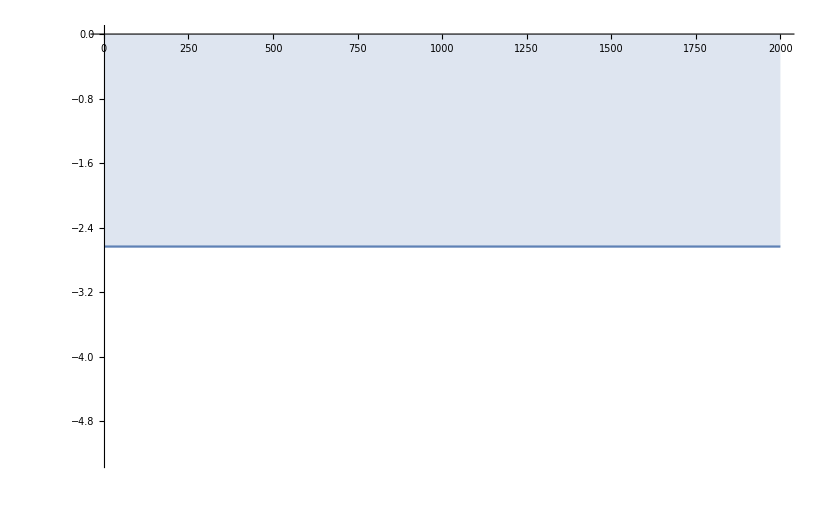
{2213.83,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled[a+2,a+1,a]-minimal,{a,2,2000,3}]]
```

```mathematica
dila[10,9,8]==dila[100,99,98]
```

False

```mathematica
normDilaFilled[10,9,8]==normDilaFilled[100,99,98]
```

True

```mathematica
N[dila[10,9,8]]
```

1.63557

```mathematica
N[dila[100,99,98]]
```

1.61803

```mathematica
tnorm[10,9,8]-boundary[10,9,8]
```

0

```mathematica
tnorm[100,99,98]-boundary[100,99,98]
```

0

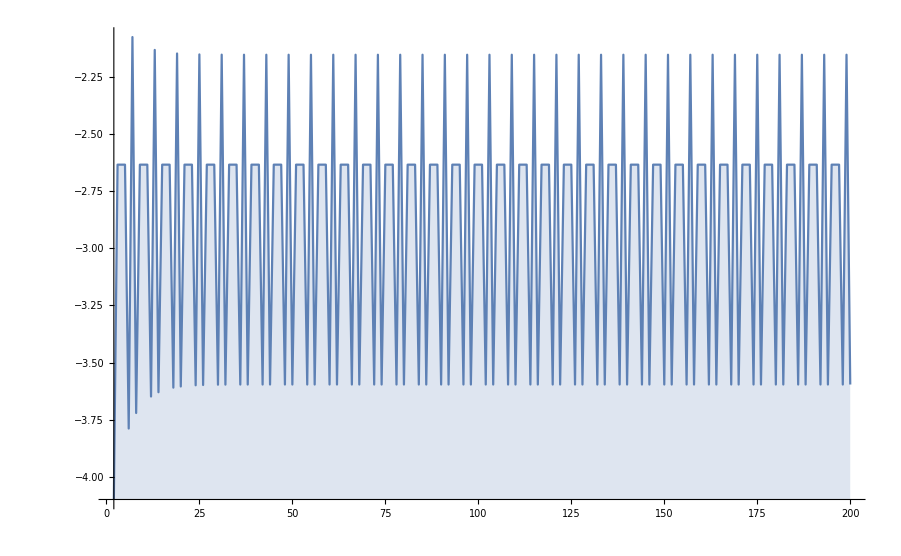
{35.5488,-Graphics-}

```mathematica
Timing[DiscretePlot[normDilaFilled[a+4,a+2,a]-minimal,{a,2,200}]]
```

```mathematica
Minimize[normDilaFilledBeta]
```

```mathematica
RegionPlot3D[x>0&&y>0&&x>z&&y>z,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
cone=ImplicitRegion[x>0&&y>0&&x>z&&y>z,{x,y,z}]
```

ImplicitRegion[x>0&&y>0&&x>z&&y>z,{x,y,z}]

```mathematica
subspace=ImplicitRegion[z==-0.5*y-x,{x,y,z}]
```

ImplicitRegion[z==-x-0.5 y,{x,y,z}]

```mathematica
test=RegionIntersection[cone,subspace]
```

ImplicitRegion[x>0&&y>0&&x>z&&y>z&&x+0.5 y+z==0,{x,y,z}]

```mathematica
Show[DiscretizeRegion[test]]
```

-Graphics3D-

```mathematica
Element[{2,2,-3},test]
```

True

```mathematica
Minimize[normDilaFilledBeta[x,y,z],{x,y,z}∈test]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1-t^x-t^y-t^(x+Times[«2»])-t^(y+Times[«2»])+t^(x+y-z)==0,t,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[1-t^y-t^(Times[«2»]+Times[«2»])+t^(0.5 y-2. z)-t^(y+Times[«2»])-t^(Times[«2»]+Times[«2»])==0,t,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[1-t^y-t^(Times[«2»]+Times[«2»])+t^(0.5 y-2. z)-t^(y+Times[«2»])-t^(Times[«2»]+Times[«2»])==0,t,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

General::stop: Further output of Solve::inex will be suppressed during this calculation.

GCD::exact: Argument -0.0860797 in GCD[-0.0860797,0.172159] is not an exact number.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GCD::exact: Argument -0.0860797 in GCD[-0.0860797,0.172159] is not an exact number.

NMinimize::nnum: The function value (2.01802-GCD[-0.0860797,0.172159]) Log[Abs[t]] is not a number at {x,y,z} = {0.879892,0.172159,-0.965972}.

Minimize[(x+y-z-GCD[y,x+z]) Log[Abs[t/.Solve[1-t^x-t^y-t^(x-z)-t^(y-z)+t^(x+y-z)==0,t,ℝ]]],{x,y,z}∈ImplicitRegion[x>0&&y>0&&x>z&&y>z&&x+0.5 y+z==0,{x,y,z}]]

```mathematica
dila[a,b,c]==dila[b,a,c]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1-t^a-t^b-t^(a+Times[«2»])-t^(b+Times[«2»])+t^(a+b-c)==0,t,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1-t^a-t^b-t^(a+Times[«2»])-t^(b+Times[«2»])+t^(a+b-c)==0,t,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

True

```mathematica
ContourPlot3D[Exp[x+y+z]-Exp[x]-Exp[y]-Exp[x-z]-Exp[y-z]+1==0,{x,y,z}∈cone]
```

-Graphics3D-